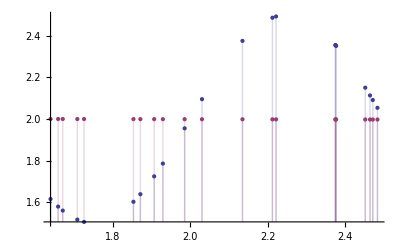

```mathematica
f[x_] = 2 + 0.5 Sin[2 Pi x];
y[w0_, w1_, z_] = w0 + w1 * z;
xVal = Part[RandomReal[{1.5,2.5}, {1, 21}], 1];
ws = FindFit[f[xVal], y[w0, w1, z], {w0, w1}, z];
ws = ws /. Rule -> List;
DiscretePlot[{f[x], y[ws[[1]], ws[[2]], x]}, {x, xVal}]
```

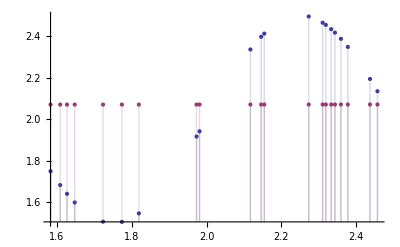

```mathematica
xVal = Part[RandomReal[{1.5,2.5}, {1, 21}], 1];
ws = FindFit[f[xVal], y[w0, w1, z], {w0, w1}, z];
ws = ws /. Rule -> List;
DiscretePlot[{f[x], y[ws[[1]], ws[[2]], x]}, {x, xVal}]
```

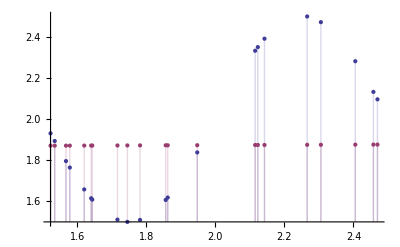

```mathematica
xVal = Part[RandomReal[{1.5,2.5}, {1, 21}], 1];
ws = FindFit[f[xVal], y[w0, w1, z], {w0, w1}, z];
ws = ws /. Rule -> List;
DiscretePlot[{f[x], y[ws[[1]], ws[[2]], x]}, {x, xVal}]
```

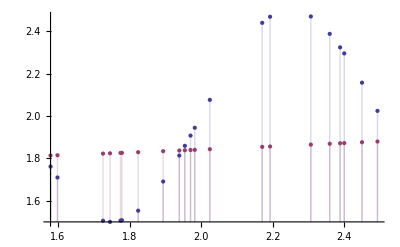

```mathematica
y1[w0_, w1_, w2_, w3_, w4_, w5_, w6_, z_] = w0 + w1 * z + w2 * z^1 + w3 * z^2 + w4 * z^3 + w5 * z^4 + w6 * z^5;
xVal = Part[RandomReal[{1.5,2.5}, {1, 21}], 1];
ws = FindFit[f[xVal], y1[w0, w1, w2, w3, w4, w5, w6 ,z], {w0, w1, w2, w3, w4, w5, w6 }, z];
ws = ws /. Rule -> List;
DiscretePlot[{f[x], y1[ws[[1]], ws[[2]],ws[[3]], ws[[4]],ws[[5]], ws[[6]],ws[[7]],  x]}, {x, xVal}]
```

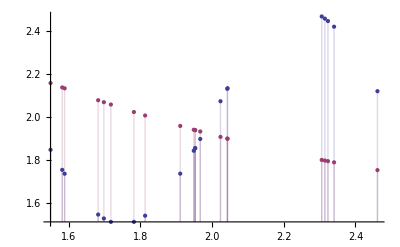

```mathematica
y1[w0_, w1_, w2_, w3_, w4_, w5_, w6_, z_] = w0 + w1 * z + w2 * z^1 + w3 * z^2 + w4 * z^3 + w5 * z^4 + w6 * z^5;
xVal = Part[RandomReal[{1.5,2.5}, {1, 21}], 1];
ws = FindFit[f[xVal], y1[w0, w1, w2, w3, w4, w5, w6 ,z], {w0, w1, w2, w3, w4, w5, w6 }, z];
ws = ws /. Rule -> List;
DiscretePlot[{f[x], y1[ws[[1]], ws[[2]],ws[[3]], ws[[4]],ws[[5]], ws[[6]],ws[[7]],  x]}, {x, xVal}]
```

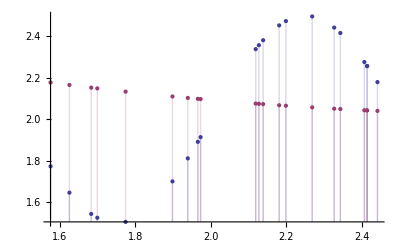

```mathematica
y1[w0_, w1_, w2_, w3_, w4_, w5_, w6_, z_] = w0 + w1 * z + w2 * z^1 + w3 * z^2 + w4 * z^3 + w5 * z^4 + w6 * z^5;
xVal = Part[RandomReal[{1.5,2.5}, {1, 21}], 1];
ws = FindFit[f[xVal], y1[w0, w1, w2, w3, w4, w5, w6 ,z], {w0, w1, w2, w3, w4, w5, w6 }, z];
ws = ws /. Rule -> List;
DiscretePlot[{f[x], y1[ws[[1]], ws[[2]],ws[[3]], ws[[4]],ws[[5]], ws[[6]],ws[[7]],  x]}, {x, xVal}]
```

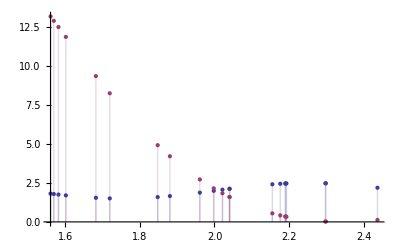

```mathematica
y2[w0_, w1_, w2_, w3_, w4_, w5_, w6_,w7_, w8_, w9_, w10_, w11_, w12_, w13_, w14_, w15_, w16_, w17_, w18_, w19_, w20_,  z_] = w0 + w1 * z^1 +  w2 * z^2 + w3 * z^3 + w4 * z^4 + w5 * z^5 + w6 * z^6 + w7 * z^7 + w8 * z^8 + w9 * z^9 + w10 * z^10 + w11 * z^11 + w12 * z^12 + w13 * z^13 + w14 * z^14 + w15 * z^15 + w16 * z^16 + w17 * z^17 + w18 * z^18 + w19 * z^19 + w20 * z^20;
xVal = Part[RandomReal[{1.5,2.5}, {1, 21}], 1];
ws = FindFit[f[xVal], y2[w0, w1, w2, w3, w4, w5, w6 , w7, w8, w9, w10, w11, w12, w13 , w14, w15, w16, w17, w18, w19, w20 ,z], {w0, w1, w2, w3, w4, w5, w6 , w7, w8, w9, w10, w11, w12, w13 , w14, w15, w16, w17, w18, w19, w20 }, z];
ws = ws /. Rule -> List;
DiscretePlot[{f[x], y2[ws[[1]], ws[[2]],ws[[3]], ws[[4]],ws[[5]], ws[[6]],ws[[7]], ws[[8]], ws[[9]],ws[[10]], ws[[11]],ws[[12]], ws[[13]],ws[[14]], ws[[15]], ws[[16]],ws[[17]], ws[[18]],ws[[19]], ws[[20]], ws[[21]],  x]}, {x, xVal}]
```

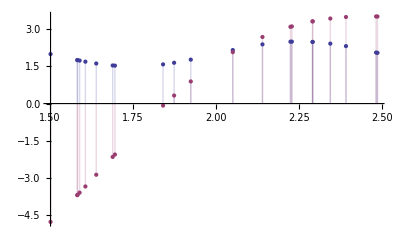

```mathematica
y2[w0_, w1_, w2_, w3_, w4_, w5_, w6_,w7_, w8_, w9_, w10_, w11_, w12_, w13_, w14_, w15_, w16_, w17_, w18_, w19_, w20_,  z_] = w0 + w1 * z^1 +  w2 * z^2 + w3 * z^3 + w4 * z^4 + w5 * z^5 + w6 * z^6 + w7 * z^7 + w8 * z^8 + w9 * z^9 + w10 * z^10 + w11 * z^11 + w12 * z^12 + w13 * z^13 + w14 * z^14 + w15 * z^15 + w16 * z^16 + w17 * z^17 + w18 * z^18 + w19 * z^19 + w20 * z^20;
xVal = Part[RandomReal[{1.5,2.5}, {1, 21}], 1];
ws = FindFit[f[xVal], y2[w0, w1, w2, w3, w4, w5, w6 , w7, w8, w9, w10, w11, w12, w13 , w14, w15, w16, w17, w18, w19, w20 ,z], {w0, w1, w2, w3, w4, w5, w6 , w7, w8, w9, w10, w11, w12, w13 , w14, w15, w16, w17, w18, w19, w20 }, z];
ws = ws /. Rule -> List;
DiscretePlot[{f[x], y2[ws[[1]], ws[[2]],ws[[3]], ws[[4]],ws[[5]], ws[[6]],ws[[7]], ws[[8]], ws[[9]],ws[[10]], ws[[11]],ws[[12]], ws[[13]],ws[[14]], ws[[15]], ws[[16]],ws[[17]], ws[[18]],ws[[19]], ws[[20]], ws[[21]],  x]}, {x, xVal}]
```

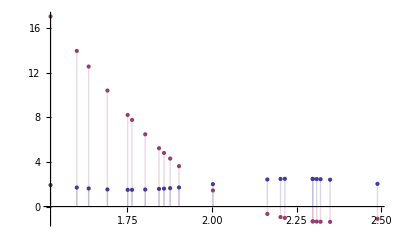

```mathematica
y2[w0_, w1_, w2_, w3_, w4_, w5_, w6_,w7_, w8_, w9_, w10_, w11_, w12_, w13_, w14_, w15_, w16_, w17_, w18_, w19_, w20_,  z_] = w0 + w1 * z^1 +  w2 * z^2 + w3 * z^3 + w4 * z^4 + w5 * z^5 + w6 * z^6 + w7 * z^7 + w8 * z^8 + w9 * z^9 + w10 * z^10 + w11 * z^11 + w12 * z^12 + w13 * z^13 + w14 * z^14 + w15 * z^15 + w16 * z^16 + w17 * z^17 + w18 * z^18 + w19 * z^19 + w20 * z^20;
xVal = Part[RandomReal[{1.5,2.5}, {1, 21}], 1];
ws = FindFit[f[xVal], y2[w0, w1, w2, w3, w4, w5, w6 , w7, w8, w9, w10, w11, w12, w13 , w14, w15, w16, w17, w18, w19, w20 ,z], {w0, w1, w2, w3, w4, w5, w6 , w7, w8, w9, w10, w11, w12, w13 , w14, w15, w16, w17, w18, w19, w20 }, z];
ws = ws /. Rule -> List;
DiscretePlot[{f[x], y2[ws[[1]], ws[[2]],ws[[3]], ws[[4]],ws[[5]], ws[[6]],ws[[7]], ws[[8]], ws[[9]],ws[[10]], ws[[11]],ws[[12]], ws[[13]],ws[[14]], ws[[15]], ws[[16]],ws[[17]], ws[[18]],ws[[19]], ws[[20]], ws[[21]],  x]}, {x, xVal}]
```